```mathematica
TOP MASS EXTRACTION;
```

```mathematica
PSEUDO DATA GENERATOR;
```

IMPORTANT VARIABLES;

```mathematica
(*mt=173.2 GeV and Scale =173,2, invarian mass of tt bar*)
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"]
Needs["HypothesisTesting`"]
mass={168.2, 170.7,173.2,175.7,178.2};
nmass=Length[mass];
number=3
crossection={951.064,930.127,906.368 ,882.925,859,733}; (*fb*)
pvaluestandard=0.0455;
```

3

```mathematica
INPUT;
```

```mathematica
luminosity =5(*fb^-1*);
numbevents=Table[crossection[[i]]*luminosity*4,{i,1,Length[crossection]}];
stdnevents =Round[IntegerPart[numbevents[[number]]]/4]
numbofdiffdist=1;
nevents=130000;
int=1;
rebinning=True;
rebin=5;
npseudobin=5;
fitf={x}
```

4532

{x}

```mathematica
NAMING SCHEME;
```

```mathematica
variable={"M_(t OverscriptBox[t, _])","p_(T, t) average", "p_(T, b OverscriptBox[b, _])", "M_b_1 average" , "M_(e^+)","M_(e^+)","M_(e^+)","min(M_(e^+),M_(e^+))","p_(T, SubscriptBox[b, 1])","p_(T, SubscriptBox[b, 2])","p_(T, b) average", "p_(T, SuperscriptBox[e, +])",
"p_(T, SuperscriptBox[μ, -])","p_(T, l) average", "p_(T, SuperscriptBox[e, +] SuperscriptBox[μ, -])","p_(T, SuperscriptBox[e, +] SubscriptBox[b, 1])","p_(T, SuperscriptBox[e, +] SubscriptBox[b, 2])", "p_(T, miss)","y_t average", "y_b average", "y_(e^+)","y_(μ^-)", "y_l average","y_(t OverscriptBox[t, _])","y_(b OverscriptBox[b, _])","ΔR_b_1","ΔR_(e^+)","ΔR_(e^+)","ΔR_(e^+)","ΔR_(μ^-)","ΔR_(μ^-)","ΔR_(t OverscriptBox[t, _])"};varnorm=Table["1/σ"<>ToString[(("d "σ)/("d" variable[[i]])),StandardForm],{i,1,Length[variable]}];
varname={"Mttbar","PTt_ave", "PTbbar","Mb1b2_ave","Me+b1","Me+b2","Me+mu-","min(Me+b1_Me+b2)","PTb1","PTb2","PTb_ave","PTe+","PTmu-","PTl_ave","PTe+mu-","PTe+b1","PTe+b2","PT_miss","yt_ave","yb_ave","ye+","ymu-","yl_ave","yttbar","ybbar","deltaRb1b2","deltaRe+mu-","deltaRe+b1","deltaRe+b2","deltaRmu-b1","deltaRmu-b2","deltaRttbar"};
scalename={"et2","mt"};
scale={"E_T/2","mt"};
lum={"5 fb^-1","35 fb^-1"};
```

```mathematica
DATA FROM HELAC (FOR STANDARD PSEUDODATA GENERATOR);
```

```mathematica
file=Table[FileNames[][[i+5]],{i,1,nmass}];
nbins=20;

start[n_]:=2+(n-1)*20
data=Block[{list},
list=Reap[Do[Sow[ReadList[file[[i]],{Number, Number, Number, Number}]],{i,1,nmass,1}]]][[2,1]];
datahist[ndiffdist_]:=Partition[Reap[Do[Block[{datalist},
datalist=Sow[data[[j,i]]];
],{j,1,nmass,1},{i, start[ndiffdist],start[ndiffdist]+nbins-1,1}]][[2,1]],nbins](*contains set of all histogram data for mtt bar for 5 different mass*)
```

```mathematica
DATA LIST ;
```

```mathematica
bins=Partition[Block[{bin},
bin=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,1]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
binwidth=Table[(Max[bins[[i]]]-Min[bins[[i]]])/(nbins-1),{i,1,nmass}];
binsreal=Reap[Do[Sow[Chop[bins[[i]]-binwidth[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsreal[[i]],Max[binsreal[[i]]]+binwidth[[i]]]],{i,1,nmass,1}]][[2,1]];
bwreal=Table[(Max[binsreal[[i]]]-Min[binsreal[[i]]])/(nbins),{i,1,nmass}];
factor=Table[Sum[vals[[j,i]],{i,1,20,1}]*bwreal[[j]]*10^-3,{j,1,nmass}]; (*area under the histogram*)

vals=Partition[Block[{val},
val=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,2]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
valsnorm=Table[vals[[i]]/(crossection[[i]]),{i,1,nmass}];(*normalised differential distribution : divided by 1/cross section *)

counts=Partition[Block[{count},
count=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,4]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
countsmax=Table[Sum[counts[[i,j]],{j,1,Length[counts[[i]]]}],{i,1,nmass}];
countsnorm=Table[counts[[i]]/countsmax[[i]],{i,1,nmass}];

error=Partition[Block[{err},
err=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,3]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
errnorm=Table[error[[i]]/(crossection[[i]]),{i,1,nmass}];
normalisation=Round[Table[Sum[valsnorm[[j,i]],{i,1,Length[valsnorm[[j]]]}]*binwidth[[j]],{j,1,nmass}]]

REBINNING;
valsnormrebin=Table[Sum[Partition[valsnorm[[j]],rebin][[i]],{i,1,Round[nbins/rebin]}]/(rebin-1),{j,1,nmass}];
errnormrebin=Table[Sum[Partition[errnorm[[j]],rebin][[i]],{i,1,Round[nbins/rebin]}]/(rebin-1),{j,1,nmass}];
countsrebin=Table[Sum[Partition[counts[[j]],rebin][[i]],{i,1,Round[nbins/rebin]}],{j,1,nmass}];
countsnormrebin=Table[Sum[Partition[countsnorm[[j]],rebin][[i]],{i,1,Round[nbins/rebin]}],{j,1,nmass}];
binsrebin=Table[Table[First[Partition[bins[[j]],Round[nbins/rebin]][[i]]],{i,1,rebin}],{j,1,nmass}];
bwrebin=Table[(Max[binsrebin[[i]]]-Min[binsrebin[[i]]])/(rebin-1),{i,1,nmass}];
binsrebinreal=Reap[Do[Sow[Chop[binsrebin[[i]]-bwrebin[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsrebinreal[[i]],Max[binsrebinreal[[i]]]+bwrebin[[i]]]],{i,1,nmass,1}]][[2,1]];
bwrebinreal=Table[(Max[binsrebinreal[[i]]]-Min[binsrebinreal[[i]]])/(rebin),{i,1,nmass}];
normalisationrebin=Round[Table[Sum[valsnormrebin[[j,i]],{i,1,Length[valsnormrebin[[j]]]}]*bwrebin[[j]],{j,1,nmass}]]
```

{1,1,1,1,1}

{1,1,1,1,1}

```mathematica
PROBABILITY DENSITY FUNCTION;
(*Weighted data by number of events*)
Which[rebinning==False,
wdata=Block[{wdata},
wdata=Reap[Do[Sow[WeightedData[bins[[i]],countsnorm[[i]]]],{i,1,nmass,1}]][[2,1]]
];
pdf=Block[{pdftest},
pdftest=Reap[Do[Sow[HistogramDistribution[wdata[[i]],{Min[binsreal[[i]]],Max[binsreal[[i]]],bwreal[[i]]}]],{i,1, nmass,1}]][[2,1]]
];,
rebinning==True,
wdata=Block[{wdata},
wdata=Reap[Do[Sow[WeightedData[binsrebin[[i]],countsnormrebin[[i]]]],{i,1,nmass,1}]][[2,1]]
];
pdf=Block[{pdftest},
pdftest=Reap[Do[Sow[HistogramDistribution[wdata[[i]],{Min[binsrebinreal[[i]]],Max[binsrebinreal[[i]]],bwrebinreal[[i]]}]],{i,1, nmass,1}]][[2,1]]
];
]
```

```mathematica
THE RATIO OF THE HELAC DATA(ALL NORMALIZED FIRST) ;
```

```mathematica
Which[rebinning==False,
ratio=Block[{maxcount,posmax,rat},
maxcount= Reap[Do[Sow[Max[countsnorm[[i]]]],{i,1,nmass,1}]][[2,1]];
posmax=Reap[Do[Sow[Flatten[Position[countsnorm[[i]],maxcount[[i]]]]],{i,1,nmass,1}]][[2,1]];
rat=Flatten[Reap[Do[Sow[(valsnorm[[i,posmax[[i]]]]*bwreal[[i]])/countsnorm[[i,posmax[[i]]]]],{i,1,nmass,1}]][[2,1]]]
];,
rebinning==True,
ratio=Block[{maxcount,posmax,rat},
maxcount= Reap[Do[Sow[Max[countsnormrebin[[i]]]],{i,1,nmass,1}]][[2,1]];
posmax=Reap[Do[Sow[Flatten[Position[countsnormrebin[[i]],maxcount[[i]]]]],{i,1,nmass,1}]][[2,1]];
rat=Flatten[Reap[Do[Sow[(valsnormrebin[[i,posmax[[i]]]]*bwrebinreal[[i]])/countsnormrebin[[i,posmax[[i]]]]],{i,1,nmass,1}]][[2,1]]]
];
]
ratio
```

{0.996088,0.995816,0.995774,0.995631,0.996166}

```mathematica
PSEUDO DATA -HISTOGRAM FITTING PROCEDURE FROM PDF (ASSUMPTION: SAME NUMBER OF BINS FROM HELAC AND RANDOM GENERATED HISTOGRAM);
```

```mathematica
HISTOGRAM GENERATED BY ARBITRARY EVENTS ACCORDING TO PDF;
```

```mathematica
histogram[nevents_,nmass_,binw_,binsreal_]:=Histogram[RandomVariate[pdf[[nmass]],nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}] (*binw needs not the same with binsreal incase of different number of bins*)
listofhistogram[nevents_,nmass_,binw_,binsreal_]:=HistogramList[RandomVariate[pdf[[nmass]],nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}]
```

```mathematica
NORMALIZATION OF HISTOGRAM;
```

```mathematica
histogramnorm[nevents_,nmass_,binw_,binsreal_,bins_]:=Histogram[WeightedData[bins[[nmass]],listofhistogram[nevents,nmass,binw,binsreal][[2]]/nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw},PlotTheme->"Detailed"]
histogramlistnorm[nevents_,nmass_,binw_,binsreal_,bins_]:=N[HistogramList[WeightedData[bins[[nmass]],listofhistogram[nevents,nmass,binw,binsreal][[2]]/nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}]]
```

```mathematica
PSEUDODATA AND PSEUDOERRORS (FROM THE BEST THEORETICAL DATA OR PREDICTION  i e INV TTBAR );
```

```mathematica
pseudopointx[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_]:=DeleteCases[histogramlistnorm[nevents,nmass,binw,binsreal,bins][[1]],Max[histogramlistnorm[nevents,nmass,binw,binsreal,bins][[1]]]]+bwreal[[nmass]]/2
pseudopointy[nevents_,nmass_,binw_,binsreal_,bins_]:=histogramlistnorm[nevents,nmass,binw,binsreal,bins][[2]]*ratio[[nmass]]/(binw) (*important to multiply by ratio!*)
pseudodata[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_]:=MapThread[{#1,#2}&,{pseudopointx[nevents,nmass,binw,binsreal,bwreal,bins],pseudopointy[nevents,nmass,binw,binsreal,bins]}]

pseudoerror[nevents_,nmass_,binw_,binsreal_,bins_,nbins_]:=Reap[Do[Sow[Sqrt[Variance[BernoulliDistribution[histogramlistnorm[nevents,nmass,binw,binsreal,bins][[2,i]]]]/nevents]*ratio[[nmass]]/(binw)],{i,1,nbins,1}]][[2,1]]
pseudo[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_,nbins_]:=Transpose[{pseudodata[nevents,nmass,binw,binsreal,bwreal,bins][[All,1]],pseudodata[nevents,nmass,binw,binsreal,bwreal,bins][[All,2]],pseudoerror[nevents,nmass,binw,binsreal,bins,nbins]}]
pseudoplot[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_,nbins_]:=ErrorListPlot[pseudo[nevents,nmass,binw,binsreal,bwreal,bins,nbins],PlotTheme->"Detailed",PlotLabel-> "Pseudodata Points",PlotStyle->Red]

normalisationpseudo=Round[Sum[y[[i]],{i,1,Length[y]}]*bwrebinreal[[3]]]
```

0

```mathematica
COMBINE HISTOGRAM FROM HELAC AND PSEUDODATA;
```

{1,1,1,1,1}

{1,1,1,1,1}

{{0.000610878,0.00117669,0.0010236,0.000777798,0.000561423},{0.000562299,0.00117291,0.00104376,0.000794267,0.000575976},{0.000520889,0.00115623,0.00106506,0.000813318,0.000593564},{0.000488747,0.00112905,0.00108521,0.000833918,0.000611554},{0.000471267,0.00109156,0.00110312,0.000856685,0.000628083}}

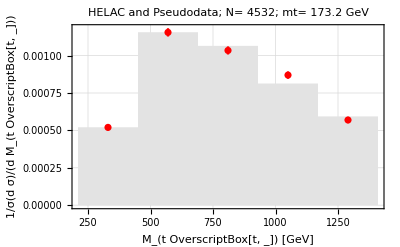

```mathematica
crossectionhel={1067.00,1040.40,1067.18,985.914,960.451};
filehel=Table[FileNames[][[i]],{i,1,nmass}];

datahel=Block[{list},
list=Reap[Do[Sow[ReadList[filehel[[i]],{Number, Number, Number, Number}]],{i,1,nmass,1}]]][[2,1]];
datahisthel[ndiffdist_]:=Partition[Reap[Do[Block[{datalist},
datalist=Sow[datahel[[j,i]]];
],{j,1,nmass,1},{i, start[ndiffdist],start[ndiffdist]+nbins-1,1}]][[2,1]],nbins](*contains set of all histogram data for mtt bar for 5 different mass*)
binshel=Partition[Block[{bin},
bin=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,1]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
binwidthel=Table[(Max[binshel[[i]]]-Min[binshel[[i]]])/(nbins-1),{i,1,5}];
binsrealhel=Reap[Do[Sow[Chop[binshel[[i]]-binwidthel[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsrealhel[[i]],Max[binsrealhel[[i]]]+binwidthel[[i]]]],{i,1,nmass,1}]][[2,1]];
bwrealhel=Table[(Max[binsrealhel[[i]]]-Min[binsrealhel[[i]]])/(nbins),{i,1,nmass}];

valshel=Partition[Block[{val},
val=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,2]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
valsnormhel=Table[valshel[[i]]/(crossectionhel[[i]]),{i,1,nmass}];(*normalised differential distribution : divided by 1/cross section *)

errorhel=Partition[Block[{err},
err=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,3]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
errnormhel=Table[errorhel[[i]]/(crossectionhel[[i]]),{i,1,nmass}];
normalisationhel=Round[Table[Sum[valsnormhel[[j,i]],{i,1,Length[valsnormhel[[j]]]}]*binwidthel[[j]],{j,1,nmass}]]

REBINNING HELAC;
valsnormrebinhel=Table[Sum[Partition[valsnormhel[[j]],rebin][[i]],{i,1,Round[nbins/rebin]}]/(rebin-1),{j,1,nmass}];
binsrebinhel=Table[Table[First[Partition[binshel[[j]],Round[nbins/rebin]][[i]]],{i,1,rebin}],{j,1,nmass}];
bwrebinhel=Table[(Max[binsrebinhel[[i]]]-Min[binsrebinhel[[i]]])/(rebin-1),{i,1,nmass}];
binsrebinrealhel=Reap[Do[Sow[Chop[binsrebinhel[[i]]-bwrebinhel[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsrebinrealhel[[i]],Max[binsrebinrealhel[[i]]]+bwrebinhel[[i]]]],{i,1,nmass,1}]][[2,1]];
bwrebinrealhel=Table[(Max[binsrebinrealhel[[i]]]-Min[binsrebinrealhel[[i]]])/(rebin),{i,1,nmass}];
errnormrebinhel=Table[Sum[Partition[errnormhel[[j]],rebin][[i]],{i,1,Round[nbins/rebin]}]/(rebin-1),{j,1,nmass}];
normalisationrebinhel=Round[Table[Sum[valsnormrebinhel[[j,i]],{i,1,Length[valsnormrebinhel[[j]]]}]*bwrebinrealhel[[j]],{j,1,nmass}]]


Which[rebinning==False,
Which[int==1,
binhelac=bins;
valhelac=valsnorm;                 (*can be different data from helac, ex: from different scale*)
binhelacreal=binsreal;
errorhelac=errnorm;
,
int==2,
binhelac=binshel;
valhelac=valsnormhel;                 (*can be different data from helac, ex: from different scale*)
binhelacreal=binsrealhel;
errorhelac=errnormhel;
],
rebinning==True,
Which[int==1,
binhelac=binsrebin;
valhelac=valsnormrebin;                 (*can be different data from helac, ex: from different scale*)
binhelacreal=binsrebinreal;
errorhelac=errnormrebin;
,
int==2,
binhelac=binsrebinhel;
valhelac=valsnormrebinhel;                 (*can be different data from helac, ex: from different scale*)
binhelacreal=binsrebinrealhel;
errorhelac=errnormrebinhel;
]
]
valhelac
histfromhelac[nmass_,bwreal_]:=Histogram[WeightedData[binhelac[[nmass]],valhelac[[nmass]]],{Min[binhelacreal[[nmass]]],Max[binhelacreal[[nmass]]],bwreal[[nmass]]},PlotTheme->"Detailed",ChartBaseStyle->EdgeForm[None],ChartStyle->GrayLevel[0.89]]
histfromhelaclist[nmass_,bwreal_]:=HistogramList[WeightedData[binhelac[[nmass]],valhelac[[nmass]]],{Min[binhelacreal[[nmass]]],Max[binhelacreal[[nmass]]],bwreal[[nmass]]}]

combine[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_,nbins_]:=Show[histfromhelac[nmass,bwreal],pseudoplot[nevents,nmass,binw,binsreal,bwreal,bins,nbins],
PlotTheme->"Detailed",
PlotLabel-> StringForm["HELAC and Pseudodata; N= ``; mt= `` GeV",nevents, mass[[nmass]]],
FrameLabel-> {StringForm["`` [GeV]",variable[[numbofdiffdist]]],StringForm["``",varnorm[[numbofdiffdist]]]}
]
Which[rebinning==False,
pt1=combine[stdnevents,3,(binwidth[[1]]*nbins/npseudobin),binsreal,bwreal,bins,nbins];,
rebinning==True,
pt1=combine[stdnevents,3,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,bwrebinreal,binsrebin,rebin];
]
pt1
```

```mathematica
THE  TOP MAS EXTRACTION PART;
```

```mathematica
FITTING THE VALUE OF DIFFERENTIAL VARIABLE FROM HELAC (THEORY) FOR EACH BIN FOR FIVE MASSES;
```

```mathematica
THEORETICAL VALUES AND ERRORS EXCEPT THE ZEROES ONE;
```

```mathematica
Which[rebinning==False,
valsnormtheo=Reap[Do[Sow[valhelac[[All,i]]],{i,1,nbins,1}]][[2,1]]*(binwidth[[1]]*nbins/npseudobin); (*the integrated value/area under the bar*)
errnormtheo=Reap[Do[Sow[errorhelac[[All,i]]],{i,1,nbins,1}]][[2,1]]*(binwidth[[1]]*nbins/npseudobin);,
rebinning==True,
valsnormtheo=Reap[Do[Sow[valhelac[[All,i]]],{i,1,rebin,1}]][[2,1]]*(bwrebin[[1]]*rebin/npseudobin); (*the integrated value/area under the bar*)
errnormtheo=Reap[Do[Sow[errorhelac[[All,i]]],{i,1,rebin,1}]][[2,1]]*(bwrebin[[1]]*rebin/npseudobin);
]

valsbindata[int_]:=Reap[Do[Sow[{{mass[[i]],valsnormtheo[[int,i]]},ErrorBar[errnormtheo[[int,i]]]}],{i,1,nmass,1}]][[2,1]]; (*for graph*)
valsbindatanozero[nbins_]:=Reap[Block[{valerr,nol},
valerr=Table[valsbindata[i],{i,1,nbins}];
nol=Table[{{mass[[k]],0.},ErrorBar[0.]},{k,1,nmass}];
Sow[DeleteCases[valerr,nol]]]][[1]];

valsbintheo[int_]:=Reap[Do[Sow[{{mass[[i]],valsnormtheo[[int,i]]},errnormtheo[[int,i]]}],{i,1,nmass,1}]][[2,1]] (*{mass,vals},err*)
valsbintheonozero[nbins_]:=Reap[Block[{valerrtheo,nol},           (*{mass,vals},err NON ZERO BIN*)
valerrtheo=Table[valsbintheo[i],{i,1,nbins}];
nol=Table[{{mass[[k]],0.},0.},{k,1,nmass}];
Sow[DeleteCases[valerrtheo, nol]]]][[1]];
Which[rebinning==False,
valsbindatanozero[nbins];
valsbintheonozero[nbins];,
rebinning==True,
valsbindatanozero[rebin];
valsbintheonozero[rebin];
]
```

```mathematica
NON ZERO BIN ENTRIES;
```

```mathematica
nonzerobin=If[MemberQ[Flatten[Transpose[valsnormtheo]],0.]==False,{"nothing"},
Block[{valstheo,errtheo,zero,nonzero,all,comp},
valstheo=Transpose[valsnormtheo];
errtheo=Transpose[errnormtheo];
zero=Reap[Do[If[valstheo[[i,j]]== 0 && errtheo[[i,j]]== 0,
Sow[{i,j}],Nothing],{i,1,nmass,1},{j,1,nbins,1}]
][[2]];
all=Flatten[Table[{Range[nmass][[i]],Range[nbins][[j]]},{i,1,nmass},{j,1,nbins}],1];
comp=Complement[all,zero[[1]]];
nonzero=If[zero≠ {},Reap[Sow[comp]],
Nothing]
][[1]]
]
```

{nothing}

```mathematica
FITTING FUNCTIONS;
```

```mathematica
value[nbins_]:=Reap[Do[Sow[valsbintheonozero[nbins][[i]][[All,1]]],{i,1,Length[valsbintheonozero[nbins]],1}]][[2,1]];
err[nbins_]:=Reap[Do[Sow[valsbintheonozero[nbins][[i]][[All,2]]],{i,1,Length[valsbintheonozero[nbins]],1}]][[2,1]];
fitting[nbins_]:=LinearModelFit[value[nbins][[#]],fitf,x,Weights->1/(err[nbins][[#]])^2]&/@ Range[1,Length[value[nbins]]];

Which[rebinning==False,
value[nbins];
err[nbins];
fitting[nbins];,
rebinning==True,
value[rebin];
err[rebin];
fitting[rebin];
]
```

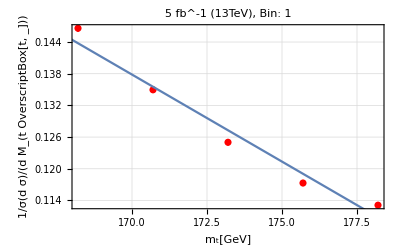
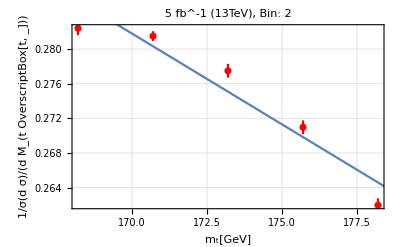
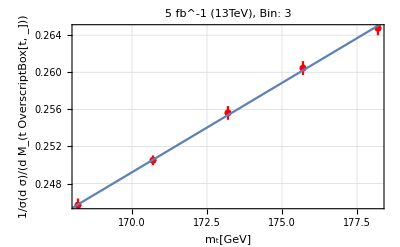
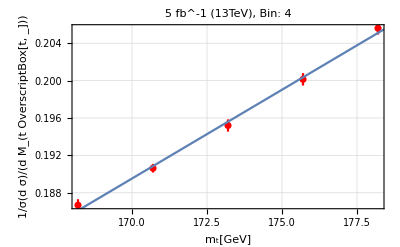
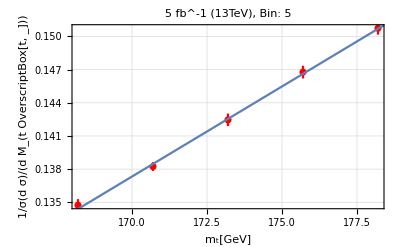

```mathematica
valsbinplot[int_,nbins_]:=ErrorListPlot[valsbindatanozero[nbins][[int]],PlotTheme->"Detailed",PlotLabel-> StringForm["`` fb^-1 (13TeV), Bin: ``",luminosity,int],PlotStyle->Red]
funcfit[int_,nbins_]:=Normal[fitting[nbins][[int]]]
funcbin[int_,nmass_,nbins_]:=funcfit[int,nbins]/.x-> mass[[nmass]]
combbinfunc[int_,nbins_]:=Block[{func},
func=funcfit[int,nbins]; (*fitting with polynomial arbitrary order*)
Show[valsbinplot[int,nbins],Plot[func,{x,160,180}],FrameLabel->{"m_t[GeV]",StringForm["``",varnorm[[numbofdiffdist]]]}]
]
allfit[nbins_]:=Table[combbinfunc[i,nbins],{i,1,Length[value[nbins]]}]
Which[rebinning==False,
allfit[nbins],
rebinning==True,
allfit[rebin]
]
```

```mathematica
PSEUDODATA VALUES AND ERRORS EXCEPT THE ZEROES ONE;
```

```mathematica
fact=Which[rebinning==False,
(binwidth[[1]]*nbins/npseudobin),
rebinning==True,
(bwrebin[[1]]*rebin/npseudobin)
];

valsnormpseudo[nevents_,binw_,binsreal_,bins_]:=Block[{valspseudo},
valspseudo=Reap[Do[Sow[pseudopointy[nevents,i,binw,binsreal,bins]*fact],{i,1,nmass,1}]][[2,1]];
Which[MemberQ[nonzerobin, "nothing"]==True,valspseudo,
MemberQ[nonzerobin, Nothing]==False,
Block[{logic},
logic=Partition[Reap[Do[
Sow[valspseudo[[nonzerobin[[i,1]],nonzerobin[[i,2]]]]],{i,1,Length[nonzerobin],1}]][[2,1]],Length[value]] (*length value=non zero bins total*)
]
]
]
errnormpseudo[nevents_,binw_,binsreal_,bins_,nbins_]:=Block[{errpseudo},
errpseudo=Reap[Do[Sow[pseudoerror[nevents,i,binw,binsreal,bins,nbins]*fact],{i,1,nmass,1}]][[2,1]];
Which[MemberQ[nonzerobin, "nothing"]==True,errpseudo,
MemberQ[nonzerobin,Nothing]==False,
Block[{logic},
logic=Partition[Reap[Do[
Sow[errpseudo[[nonzerobin[[i,1]],nonzerobin[[i,2]]]]],{i,1,Length[nonzerobin],1}]][[2,1]],Length[value]]
]
]
]

PSEUDODATA USED FOR GENERATING THE CHISQUARE;
Which[rebinning==False,
valuep=valsnormpseudo[stdnevents,(binwidth[[1]]*nbins/npseudobin),binsreal,bins][[number]];
errorp=errnormpseudo[stdnevents,(binwidth[[1]]*nbins/npseudobin),binsreal,bins,nbins][[number]];,
rebinning==True,
valuep=valsnormpseudo[stdnevents,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin][[number]];
errorp=errnormpseudo[stdnevents,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin,rebin][[number]];
]
(*pseudo data used only using the 173.2 GeV and dynamical Scale as the best theoretical prediction*)
```

```mathematica
THE χ^2 PROCEDURE;
```

173.638

{171.365,175.912}

2.27343

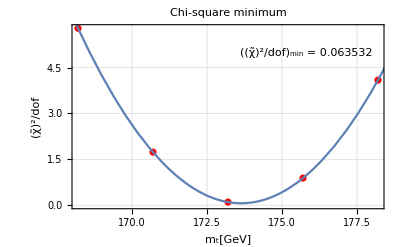

173.638±2.27343

```mathematica
CHI SQUARE STUFF;

chisquarebin[pvalue_,perror_,int_,mass_,nbins_]:=N[(pvalue[[int]]-fitting[nbins][[int]][mass])^2/(perror[[int]]^2)];
sumchisquare[pvalue_,perror_,mass_,nbins_]:=N[Sum[chisquarebin[pvalue,perror,i,mass,nbins],{i,1,Length[pvalue]-1}]];
chitilde[pvalue_,perror_,mass_,nbins_]:=N[sumchisquare[pvalue,perror,mass,nbins]/(Length[pvalue]-1)]
minchitilde[pvalue_,perror_,nbins_]:=x/.Last[FindMinimum[chitilde[pvalue,perror,x,nbins],{x,168.2,178.2}]]

Which[rebinning==False,
chidata=ParallelTable[{mass[[j]],Table[chitilde[valuep,errorp,mass[[i]],nbins],{i,1,nmass}][[j]]},{j,1,nmass}];
minimumx=minchitilde[valuep,errorp,nbins];
minchi=chitilde[valuep,errorp,minimumx,nbins];
chivaluebnd=minchi+1;,
rebinning==True,
chidata=ParallelTable[{mass[[j]],Table[chitilde[valuep,errorp,mass[[i]],rebin],{i,1,nmass}][[j]]},{j,1,nmass}];
minimumx=minchitilde[valuep,errorp,rebin];
minchi=chitilde[valuep,errorp,minimumx,rebin];
chivaluebnd=minchi+1;
]
chifunc=LinearModelFit[chidata,{1,x,x^2},x];
minimumx

deltamassbnd=x/.Solve[Normal[chifunc]==chivaluebnd,x] (*finding the corresponding m value for given chi square value without divide by dof*)
deltam1=Max[Abs[minimumx-deltamassbnd]]
Which[rebinning==False,
chiparabola=Show[ListPlot[chidata,FrameLabel-> {"m_t[GeV]","(χ̃)^2/dof"},PlotTheme->"Detailed",PlotStyle->Red],Plot[Normal[chifunc],{x,160,180}],PlotLabel->"Chi-square minimum",Epilog-> Inset[Framed[Style["((χ̃)^2/dof)_min = " <> ToString[minchi]],Background->White],Scaled[{.75,.85}]]],
rebinning==True,
chiparabola=Show[ListPlot[chidata,FrameLabel-> {"m_t[GeV]","(χ̃)^2/dof"},PlotTheme->"Detailed",PlotStyle->Red],Plot[Normal[chifunc],{x,160,180}],PlotLabel->"Chi-square minimum",Epilog-> Inset[Framed[Style["((χ̃)^2/dof)_min = " <> ToString[minchi]],Background->White],Scaled[{.75,.85}]]]
]
PlusMinus[minimumx,deltam1]
```

```mathematica
BEFORE DIVIDED BY DEGREE OF FREEDOMS (EXTRACTING ONE DELTA MASS);
```

{172.501,174.775}

1.13672

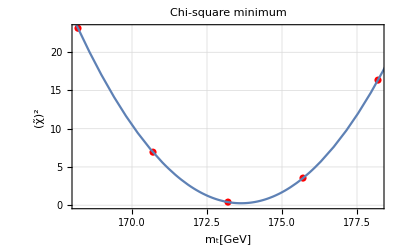

173.638±1.13672

```mathematica
minchitilderaw[pvalue_,perror_,nbins_]:=x/.Last[FindMinimum[sumchisquare[pvalue,perror,x,nbins],{x,168.2,178.2}]]
Which[rebinning==False,
chidataraw=ParallelTable[{mass[[j]],Table[sumchisquare[valuep,errorp,mass[[i]],nbins],{i,1,nmass}][[j]]},{j,1,nmass}];
mmiddle=minchitilderaw[valuep,errorp,nbins];
minchiraw=sumchisquare[valuep,errorp,mmiddle,nbins];
chivaluebound=minchiraw+1;,
rebinning==True,
chidataraw=ParallelTable[{mass[[j]],Table[sumchisquare[valuep,errorp,mass[[i]],rebin],{i,1,nmass}][[j]]},{j,1,nmass}];
mmiddle=minchitilderaw[valuep,errorp,rebin];
minchiraw=sumchisquare[valuep,errorp,mmiddle,rebin];
chivaluebound=minchiraw+1;
]

chifuncraw=LinearModelFit[chidataraw,{1,x,x^2},x];
deltamassbound=x/.Solve[Normal[chifuncraw]==chivaluebound,x] (*finding the corresponding m value for given chi square value without divide by dof*)
deltamone=Max[Abs[mmiddle-deltamassbound]]

Which[rebinning==False,
chiparabolaraw=Show[ListPlot[chidataraw,FrameLabel-> {"m_t[GeV]","(χ̃)^2"},PlotTheme->"Detailed",PlotStyle->Red],Plot[Normal[chifuncraw],{x,160,180}],PlotLabel->"Chi-square minimum"],
rebinning==True,
chiparabolaraw=Show[ListPlot[chidataraw,FrameLabel-> {"m_t[GeV]","(χ̃)^2"},PlotTheme->"Detailed",PlotStyle->Red],Plot[Normal[chifuncraw],{x,160,180}],PlotLabel->"Chi-square minimum"]
]
PlusMinus[mmiddle,deltamone]
```

```mathematica
FITTED MASS ;
```

{167.145,170.5,173.951,176.335,178.337}

{1.20901,1.17619,1.15602,1.11164,1.11798}

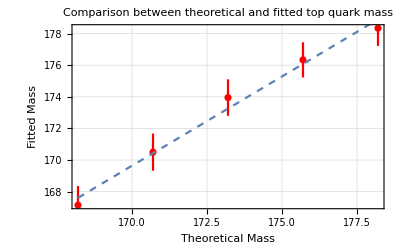

```mathematica
fittingmass[nevents_,binw_,binsreal_,bins_,nbins_,m_]:=Reap[
Block[{pvaluelist,perrorlist,zeropos,datachi,chisq,mout,result,chisqraw,datachiraw,fchiraw,chibound,deltambound,deltameins},
pvaluelist=valsnormpseudo[nevents,binw,binsreal,bins][[m]];
perrorlist=errnormpseudo[nevents,binw,binsreal,bins,nbins][[m]] ;
zeropos=Position[perrorlist,0.]; 
perrorlist=Delete[perrorlist,zeropos]; (*delete zero error values*)
pvaluelist=Delete[pvaluelist,zeropos];
chisq=ParallelTable[chitilde[pvaluelist,perrorlist,mass[[i]],nbins],{i,1,nmass}];
chisqraw=ParallelTable[sumchisquare[pvaluelist,perrorlist,mass[[i]],nbins],{i,1,nmass}];
datachi=ParallelTable[{mass[[j]],chisq[[j]]},{j,1,nmass}];
datachiraw=ParallelTable[{mass[[j]],chisqraw[[j]]},{j,1,nmass}];
fchiraw=LinearModelFit[datachiraw,{1,x,x^2},x];
mout=minchitilderaw[pvaluelist,perrorlist,nbins];
chibound=sumchisquare[pvaluelist,perrorlist,minchitilderaw[pvaluelist,perrorlist,nbins],nbins]+1;
deltambound=x/.Solve[Normal[fchiraw]==chibound,x];
deltameins=Max[Abs[mout-deltambound]];
result=Sow[{mout,deltameins}]
]
][[2,1]];
Which[rebinning==False,
massfit=Reap[Do[Sow[fittingmass[stdnevents,(binwidth[[1]]*nbins/npseudobin),binsreal,bins,nbins,i]],{i,1,nmass,1}]][[2,1]];,
rebinning==True,
massfit=Reap[Do[Sow[fittingmass[stdnevents,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin,rebin,i]],{i,1,nmass,1}]][[2,1]];
]
masschi=Reap[Do[Sow[Flatten[massfit[[i]],1]],{i,1,nmass,1}]][[2,1]];
fitmass=masschi[[All,1]]
fitmasserr=masschi[[All,2]]

PLOTTING THE THEORETICAL MASS AND THE MASS FROM CHI SQUARE + 1 ANALYSIS  FROM ONE PSEUDO EXPERIMENTS(NO BIASED);
fitmassplot=ErrorListPlot[Table[{{mass[[i]],fitmass[[i]]},ErrorBar[fitmasserr[[i]]]},{i,1,nmass}],PlotTheme->"Detailed",PlotStyle->Red];
fitmassfunc=Fit[Table[{mass[[i]],fitmass[[i]]},{i,1,nmass}],{1,x},x];
fittmass=Show[fitmassplot,Plot[fitmassfunc,{x,168.2,178.2},PlotStyle->Dashed],PlotTheme->"Detailed",FrameLabel-> { "Theoretical Mass","Fitted Mass"},PlotLabel-> "Comparison between theoretical and fitted top quark mass"]
```

```mathematica
N -PSEUDO EXPERIMENTS;
```

```mathematica
npseudoexp[nevents_,binw_,binsreal_,bins_,nbins_,n_]:=Partition[Reap[
For[k=1,k<n+1,k++,
Block[{pvaluelist,perrorlist,zeropos,datachi,chisq,mout,chisqmin,result,chisqminraw},
pvaluelist=valsnormpseudo[nevents,binw,binsreal,bins][[number]];
perrorlist=errnormpseudo[nevents,binw,binsreal,bins,nbins][[number]] ;
zeropos=Position[perrorlist,0.]; 
perrorlist=Delete[perrorlist,zeropos]; (*delete zero error values*)
pvaluelist=Delete[pvaluelist,zeropos];
chisq=ParallelTable[chitilde[pvaluelist,perrorlist,mass[[i]],nbins],{i,1,nmass}];
datachi=ParallelTable[{mass[[j]],chisq[[j]]},{j,1,nmass}];
mout=minchitilderaw[pvaluelist,perrorlist,nbins];
chisqmin=chitilde[pvaluelist,perrorlist,mout,nbins];
chisqminraw=sumchisquare[pvaluelist,perrorlist,mout,nbins];
result=Sow[{mout,chisqmin,chisqminraw}]
]
];
][[2,1]],n];
Which[rebinning==False,
exp=Reap[Sow[npseudoexp[stdnevents,(binwidth[[1]]*nbins/npseudobin),binsreal,bins,nbins,100]]][[2,1,1,1]];,
rebinning==True,
exp=Reap[Sow[npseudoexp[stdnevents,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin,rebin,100]]][[2,1,1,1]];
]
```

```mathematica
SOME STATISTICS AND  HISTOGRAMS ABOUT PSEUDO EXPERIMENT;
```

{175.313,173.374,175.36,174.876,173.036,172.436,172.135,171.664,173.417,171.3,172.19,175.254,175.711,174.477,174.5,173.011,173.744,171.313,170.84,173.14,173.771,172.543,173.733,173.643,173.524,173.365,172.57,176.046,175.527,173.558,174.006,175.606,174.793,174.316,172.009,172.871,173.069,172.333,173.474,175.644,174.337,173.717,175.006,172.736,175.165,174.984,174.162,176.24,172.464,172.059,172.024,171.548,173.685,174.418,177.635,174.364,173.45,173.147,171.24,172.74,175.397,174.273,173.136,174.742,174.491,172.246,173.118,175.189,175.204,170.862,173.044,173.293,174.493,175.794,172.227,173.573,171.727,172.28,173.007,177.164,171.335,174.499,174.045,174.128,172.926,174.241,174.231,171.275,176.159,174.405,174.036,174.081,172.915,173.567,171.51,173.636,172.889,172.634,174.835,173.994}

{2.33079,0.18441,0.511179,1.59764,1.05176,0.993553,0.458278,0.0693058,0.645855,1.11644,0.106129,0.224835,1.07071,0.0527736,1.11653,0.288948,1.65769,0.875167,0.948223,1.16168,0.178498,0.990865,0.268822,0.50429,0.126048,0.733752,0.290711,0.502753,0.971607,0.259774,0.304876,0.212743,0.367345,0.324984,1.28441,0.052858,0.895809,1.10972,0.329038,0.444341,0.203732,1.08265,1.46094,1.09958,1.26918,0.936745,0.90229,0.391748,0.01888,1.96486,0.617281,0.543432,1.0354,1.68091,0.979931,1.58065,0.738796,1.98419,1.37046,0.136502,0.0899016,0.120257,1.09425,2.66234,1.24716,0.0969892,0.238286,0.018726,0.107711,1.23144,0.0685989,0.102901,0.606806,1.98885,1.29575,2.48841,2.13192,1.28418,0.184794,0.00516978,0.177493,0.704513,0.871401,0.729887,0.347382,2.20748,0.244966,0.223386,1.75881,0.438809,0.740306,0.199711,0.625692,0.299014,0.850659,0.6479,0.517077,0.238066,5.25907,0.0257926}

{9.32316,0.73764,2.04472,6.39055,4.20703,3.97421,1.83311,0.277223,2.58342,4.46574,0.424516,0.899341,4.28283,0.211094,4.4661,1.15579,6.63077,3.50067,3.79289,4.64671,0.713994,3.96346,1.07529,2.01716,0.504194,2.93501,1.16284,2.01101,3.88643,1.0391,1.2195,0.850973,1.46938,1.29994,5.13763,0.211432,3.58324,4.43887,1.31615,1.77736,0.814926,4.33061,5.84375,4.39834,5.0767,3.74698,3.60916,1.56699,0.07552,7.85943,2.46913,2.17373,4.14161,6.72365,3.91973,6.3226,2.95518,7.93675,5.48186,0.546009,0.359606,0.48103,4.37701,10.6494,4.98863,0.387957,0.953142,0.0749042,0.430843,4.92576,0.274396,0.411604,2.42723,7.95539,5.183,9.95366,8.52767,5.13671,0.739175,0.0206791,0.709973,2.81805,3.48561,2.91955,1.38953,8.82992,0.979866,0.893544,7.03524,1.75524,2.96122,0.798846,2.50277,1.19606,3.40264,2.5916,2.06831,0.952263,21.0363,0.10317}

{0.00950494,0.016202,0.0327582,0.0647484,0.0794974,0.0811712,0.0847344,0.0916698,0.0938398,0.119256,0.127906,0.17839,0.202047,0.235487,0.278399,0.287131,0.341409,0.353799,0.359311,0.383803,0.392989,0.428457,0.475387,0.504937,0.509836,0.512326,0.516182,0.534338,0.579077,0.582878,0.589318,0.608237,0.615831,0.620413,0.640656,0.644857,0.663387,0.684479,0.712195,0.726393,0.737166,0.753115,0.763294,0.765381,0.781088,0.82518,0.838771,0.841078,0.846559,0.848277,0.912477,0.916488,1.01786,1.08218,1.08953,1.1088,1.14137,1.18323,1.18858,1.21645,1.22411,1.3196,1.33164,1.35409,1.37221,1.40588,1.42529,1.46184,1.51274,1.51693,1.53684,1.55194,1.5933,1.60221,1.62848,1.64264,1.6608,1.7077,1.74529,1.87533,1.92547,1.95388,1.98765,1.99203,2.05898,2.1043,2.14178,2.14255,2.31755,2.33887,2.35216,2.37745,2.39363,2.41179,2.5072,2.58832,2.79043,2.81245,3.51186,3.98331}

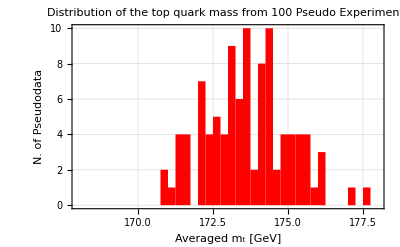

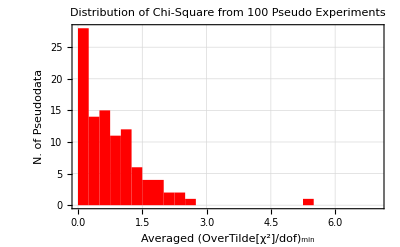

True

Theory, LO QCD | Variable | Luminosity [fb^-1] | m_t±δm_t[GeV] | Averaged ((χ̃)^2/dof)_min | Probability p-value | m_t^in-m_t^out [GeV]
Full, μ_0=E_T/2 | M_(t OverscriptBox[t, _]) | 5 | 173.652±1.46184 | 0.807851 | 0.480127 | -0.452124

```mathematica
pexpmass=exp[[All,1]]
pexpchisq=exp[[All,2]]
exp[[All,3]]

massout=Mean[exp[[All,1]]];

stddeviations=Reap[Do[
Sow[StandardDeviation[exp[[All,1]]]],
{i,1,Length[exp],1}]][[2,1]];

deltamassout=Reap[Block[{sortedmass,variance},
sortedmass=exp[[All,1]];
variance=Sort[Reap[Do[Sow[Abs[sortedmass[[i]]-Mean[sortedmass]]],{i,1,Length[sortedmass],1}]][[2,1]]]; (*sorted the spread of the data from the mean*)
Print[variance];
Sow[variance[[Round[68*Length[sortedmass]/100]]]] (*take the 68% CL i.e take the 68%*Number-th of the data as the error*)
]][[2,1,1]];

chiout=Mean[exp[[All,2]]];

pexpmasshist=Histogram[pexpmass,{168,178,0.25},PlotTheme->"Detailed",FrameLabel->{"Averaged m_t [GeV]","N. of Pseudodata"},ChartBaseStyle->EdgeForm[None], ChartStyle->Red, PlotLabel-> "Distribution of the top quark mass from 100 Pseudo Experiments"]
pexpchisqhist=Histogram[pexpchisq,{0,7,0.25},PlotTheme->"Detailed",FrameLabel-> {"Averaged (OverTilde[χ^2]/dof)_min", "N. of Pseudodata"},ChartBaseStyle->EdgeForm[None], ChartStyle->Red,PlotLabel-> "Distribution of Chi-Square from 100 Pseudo Experiments"]

SOME RESULTS;

pvalue[pvalue_]:= ChiSquarePValue[chiout*(Length[pvalue]-1),Length[pvalue]-1][[2]];
pvout=pvalue[valuep];
pvout>pvaluestandard
(*stddeviations=(Abs[massout[[number]]]*Sqrt[Length[pexpmass]/2])/InverseErfc[pvout]*10^-3*)
deltam=mass[[number]]-massout;
result=Grid[{{"Theory, LO QCD", "Variable","Luminosity [fb^-1]",ToString[PlusMinus[Subscript[m, t],Subscript[δm, t]],StandardForm]<>"[GeV]", "Averaged ((χ̃)^2/dof)_min","Probability p-value","m_t^in-m_t^out [GeV]"},
{StringForm["Full, μ_0=``",scale[[int]]],variable[[numbofdiffdist]],luminosity,PlusMinus[N[massout,2],N[deltamassout,2]],chiout,pvout ,deltam}},Frame->All]
```

```mathematica
EXPORTING FIGURES;
```

```mathematica
(*Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_pseudodata_"<>ToString[nevents,StandardForm]<>".pdf",pt1];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_pseudodata_"<>ToString[nevents/4,StandardForm]<>".pdf",pt2];*)
Which[rebinning==False,
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_pseudo_vs_theo_each_bin.pdf",allfit[nbins]];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_parabola_chi_square.pdf",chiparabola];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_pseudo_exp_mass_averaged.pdf", pexpmasshist];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_pseudo_exp_chi_square_averaged.pdf",pexpchisqhist];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_mass fitting.pdf", fittmass];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_result_table.pdf", result];,
rebinning==True,
(*Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[luminosity]<>"_pseudodata"<>".pdf",pt1];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[luminosity]<>"_pseudo_vs_theo_each_bin.pdf",allfit[rebin]];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[luminosity]<>"_parabola_chi_square.pdf",chiparabola];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[luminosity]<>"_pseudo_exp_mass_averaged.pdf", pexpmasshist];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[luminosity]<>"_pseudo_exp_chi_square_averaged.pdf",pexpchisqhist];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[luminosity]<>"_mass fitting.pdf", fittmass];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[luminosity]<>"_result_table.pdf", result];*)
]
```